# C - x^-4 smear

## cosine trap switch, x^-4 smear, plot <g|ρ|g> as a function of length scale of the smearing, with detector beginning in |g><g|

## set some parameters

```mathematica
α=1;
```

```mathematica
numSteps=20;
```

```mathematica
Ω=1;
```

#### set values of σ;write σ in terms ofσ_0~10^-4/Ω

```mathematica
Subscript[σ, 0]=10^-4/Ω;
```

```mathematica
(*use these values for calculations*)
numSteps=200;
σMin=0.1 Subscript[σ, 0];  σMax=2 Subscript[σ, 0];  σStepSize=Abs[σMin-σMax]/numSteps;
σValues=Table[σ,{σ,σMin,σMax,σStepSize}];
```

```mathematica
(*then plot <g|ρ|g> versus σNorm=σ/Subscript[σ, 0]*)
σNormValues=σValues/Subscript[σ, 0];
```

```mathematica
clear[λ];
```

## the smearing function

```mathematica
f[x_,σ_]:=(σ^3 √2)/π 1/(x^4+σ^4)
ftil[k_,σ_]:=FourierTransform[f[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftil[k,σ]
```

(1/2+ⅈ/2) ⅇ^(-((1+ⅈ) k σ)/(√2)) (ⅇ^(√2 k σ) (-ⅈ+ⅇ^(ⅈ √2 k σ)) HeavisideTheta[-k]+(1-ⅈ ⅇ^(ⅈ √2 k σ)) HeavisideTheta[k])

## the switching function

```mathematica
chiT1[t_]:=A/2*(1+Cos[r/π(t+c)])
chiT2[t_]:=A
chiT3[t_]:=A/2*(1+Cos[r/π(t-c)])
```

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-c-r,-c}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-c,c}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,c,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,c,c+r}]
```

## the k integrand

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_,σ_]:=-1/π ⅇ^(-ε*k)*k*ftil[k,σ]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## the numerical transition probability

```mathematica
c=2;r=0.2;Ω=1;
A=(2*c+r+(4π)/r*Sin[r^2/(4π)])^-1;
```

### with an ε regularized cutoff (exp)

```mathematica
ε=0.2;
```

```mathematica
pexpx4=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

### with no cutoff (ε:=0)

```mathematica
ε=0;
```

```mathematica
pnonex4=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

NIntegrate::deorela: The relative error 3.31809 is larger than expected for the integrand -ⅈ\ ⅇ^-√2\ k\ k\ Cos[√2\ k]\ (ⅇ^√2\ k\ « 1 »\ HeavisideTheta[-k] + « 1 »)^2\ (Sin[2 - 2\ k]^2/(« 1 »)^2 + Sin[2\ (1 + k)]^2/(« 18 »  + « 18 »\ k)^2 + tInt1[k] + tInt3[k])/2\ π
 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

NIntegrate::deorela: The relative error 3.0647 is larger than expected for the integrand -ⅈ\ ⅇ^-21\ k/10\ √2\ k\ Cos[21\ k/10\ √2]\ (ⅇ^« 1 »/« 1 »\ (-ⅈ + « 1 »)\ « 14 »[-k] + « 1 »)^2\ (Sin[2 - 2\ k]^2/(« 1 »)^2 + Sin[2\ (1 + k)]^2/(« 18 »  + « 18 »\ k)^2 + tInt1[k] + tInt3[k])/2\ π
 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

NIntegrate::deorela: The relative error 2.83232 is larger than expected for the integrand -ⅈ\ ⅇ^-11\ k/5\ √2\ k\ Cos[11\ k/5\ √2]\ (ⅇ^« 1 »/« 1 »\ (-ⅈ + « 1 »)\ « 14 »[-k] + « 1 »)^2\ (Sin[2 - 2\ k]^2/(« 1 »)^2 + Sin[2\ (1 + k)]^2/(« 18 »  + « 18 »\ k)^2 + tInt1[k] + tInt3[k])/2\ π
 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

General::stop: Further output of NIntegrate :: deorela will be suppressed during this calculation.

### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
ε=0;  cutoff=5*Ω;
```

```mathematica
psharpx4=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,cutoff}],{σ,σMin,σMax,σStepSize}];
```

## plot p v σ

```mathematica
λ=0.1;
```

#### put the data into lists for plotting

```mathematica
dataExpCutoffx4     =Transpose[{σNormValues,pexpx4}];
dataNoCutoffx4       =Transpose[{σNormValues,pnonex4}];
dataSharpCutoffx4=Transpose[{σNormValues,psharpx4}];
```

```mathematica
Export["C:\Users\Public\Documents\emma\udw-detector-shape\Cosine Trap Switching\dataExpCutoffx4.csv",dataExpCutoffx4];
Export["C:\Users\Public\Documents\emma\udw-detector-shape\Cosine Trap Switching\dataNoCutoffx4.csv",dataNoCutoffx4];
Export["C:\Users\Public\Documents\emma\udw-detector-shape\Cosine Trap Switching\dataSharpCutoffx4.csv",dataSharpCutoffx4];
```

### ploot

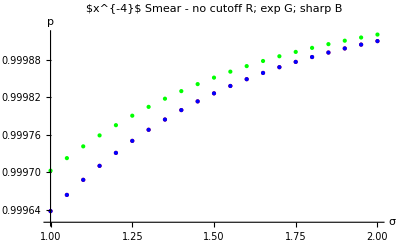

```mathematica
ListPlot[{dataNoCutoffx4,dataExpCutoffx4,dataSharpCutoffx4},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["$x^{-4}$ Smear - no cutoff R; exp G; sharp B",FontSize->16]]
```

### plot relative difference to p_δ